```mathematica
Ev:={0,E0}
r[x_,y_]:={x,y}
R:=1
E0:=1
```

```mathematica
ϕk[x_,y_,ϵg_,ϵk_]:=-(1-(ϵg-ϵk)/(ϵg+2*ϵk)*R^3/((x^2+y^2)^(3/2)))*(Ev.r[x,y])
ϕb[x_,y_,ϵg_,ϵk_]:=-3*ϵk/(ϵg+2*ϵk)*(Ev.r[x,y])
ϕmk[x_,y_,ϵg_,ϵk_]:=(ϵg-ϵk)/(ϵg+2*ϵk)*R^3/((x^2+y^2)^(3/2))*(Ev.r[x,y])
ϕmb[x_,y_,ϵg_,ϵk_]:=-(ϵk-ϵg)/(ϵg+2*ϵk)*(Ev.r[x,y])
```

```mathematica
ϕ[x_,y_,ϵg_,ϵk_]:=Piecewise[{{ϕk[x,y,ϵg,ϵk],x^2+y^2>=R^2},{ϕb[x,y,ϵg,ϵk],x^2+y^2<R^2}}]
Evv[x_,y_,ϵg_,ϵk_]:=Piecewise[{{{-D[ϕk[xx,y,ϵg,ϵk],xx]/.xx->x,-D[ϕk[x,yy,ϵg,ϵk],yy]/.yy->y},x^2+y^2>=R^2},{{-D[ϕb[xx,y,ϵg,ϵk],xx]/.xx->x,-D[ϕb[x,yy,ϵg,ϵk],yy]/.yy->y},x^2+y^2<R^2}}]
Evvk[x_,y_,ϵg_,ϵk_]:=Piecewise[{{{-D[ϕk[xx,y,ϵg,ϵk],xx]/.xx->x,-D[ϕk[x,yy,ϵg,ϵk],yy]/.yy->y},x^2+y^2>=R^2}}]
Evvb[x_,y_,ϵg_,ϵk_]:=Piecewise[{{{0,0},x^2+y^2>=R^2},{{-D[ϕb[xx,y,ϵg,ϵk],xx]/.xx->x,-D[ϕb[x,yy,ϵg,ϵk],yy]/.yy->y},x^2+y^2<R^2}}]
ϕmm[x_,y_,ϵg_,ϵk_]:=Piecewise[{{ϕmk[x,y,ϵg,ϵk],x^2+y^2>=R^2},{ϕmb[x,y,ϵg,ϵk],x^2+y^2<R^2}}]
Emm[x_,y_,ϵg_,ϵk_]:=Piecewise[{{{-D[ϕmk[xx,y,ϵg,ϵk],xx]/.xx->x,-D[ϕmk[x,yy,ϵg,ϵk],yy]/.yy->y},x^2+y^2>=R^2},{{-D[ϕmb[xx,y,ϵg,ϵk],xx]/.xx->x,-D[ϕmb[x,yy,ϵg,ϵk],yy]/.yy->y},x^2+y^2<R^2}}]
ϕM[x_,y_,ϵg_,ϵk_]:=Piecewise[{{0,x^2+y^2>=R^2},{ϕmb[x,y,ϵg,ϵk],x^2+y^2<R^2}}]
M[x_,y_,ϵg_,ϵk_]:=Piecewise[{{{0,0},x^2+y^2>=R^2},{{-D[ϕmb[xx,y,ϵg,ϵk],xx]/.xx->x,-D[ϕmb[x,yy,ϵg,ϵk],yy]/.yy->y},x^2+y^2<R^2}}]
```

ek>eb következik

```mathematica
points=Flatten[Table[{i,j},{i,-1.5,1.5,0.3},{j,{-1.45,1.45}}],1];
pointsE=Flatten[Table[{i,0},{i,-1+1/8,1-1/8,2/8}],0]
pointsb=Flatten[{Table[{i,0},{i,-0.8,0.8,0.4}],{{0,1.1},{0,-1.1},{-1,0.57},{1,0.57},{-1,-0.57},{1,-0.57},{-0.47,1},{-0.47,-1},{0.47,1},{0.47,-1}}},1]
```

{{-7/8,0},{-5/8,0},{-3/8,0},{-1/8,0},{1/8,0},{3/8,0},{5/8,0},{7/8,0}}

{{-0.8,0},{-0.4,0},{0.,0},{0.4,0},{0.8,0},{0,1.1},{0,-1.1},{-1,0.57},{1,0.57},{-1,-0.57},{1,-0.57},{-0.47,1},{-0.47,-1},{0.47,1},{0.47,-1}}

```mathematica
Export["~/Dokumentumok/Pk.png",Show[ContourPlot[x^2+y^2==1,{x,-1.55,1.55},{y,-1.55,1.55},ContourStyle->{Black,Thick}],StreamPlot[Emm[x,y,1,3],{x,-1.55,1.55},{y,-1.55,1.55},
StreamScale->Full,
StreamStyle->{"Line",Thick},
StreamPoints->{pointsb,Automatic}],Frame->None],ImageResolution->300]
```

~/Dokumentumok/Pk.png

```mathematica
Export["~/Dokumentumok/Dk.png",
Show[ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->{Black,Filling->Bottom,Thick}],StreamPlot[Evv[x,y,1,3],{x,-1.5,1.5},{y,-1.5,1.5},
StreamScale->Full,
StreamStyle->{"Line",Thick},
StreamPoints->{points,Automatic}],Frame->None,Background->None],ImageResolution->300]
Export["~/Dokumentumok/Ek.png",
Show[ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->{Black,Filling->Bottom,Thick},Background->None],Graphics[{White,Disk[{0,0},1]}],ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->{Black,Filling->Bottom,Thick}],(*StreamPlot[Evvk[x,y,1,3],{x,-1.5,1.5},{y,-1.5,1.5},
StreamScale->Full,
StreamStyle->{"Line",Thick},
StreamPoints->{points,Automatic},PerformanceGoal->"Quality"],*)
StreamPlot[Evvb[x,y,1,3],{x,-1.5,1.5},{y,-1.5,1.5},StreamScale->Full,
StreamStyle->{"Line",Thick},
StreamPoints->{pointsE,Automatic},PerformanceGoal->"Quality",Background->None],Frame->None,Background->None],Background->None,ImageResolution->300]
```

~/Dokumentumok/Dk.png

~/Dokumentumok/Ek.png

ek<eb következik

```mathematica
points2=Flatten[Table[{i,j},{i,-1.5,1.5,0.3},{j,{1.45,1.45}}],1]
pointsE2=Flatten[Table[{i,0},{i,-1+1/6,1-1/6,2/6}],0]
pointsb2=Flatten[{Table[{i,0},{i,-0.8,0.8,0.4}],{{0,1.1},{0,-1.1},{-1,0.57},{1,0.57},{-1,-0.57},{1,-0.57},{-0.47,1},{-0.47,-1},{0.47,1},{0.47,-1}}},1]
```

{{-1.5,1.45},{-1.5,1.45},{-1.2,1.45},{-1.2,1.45},{-0.9,1.45},{-0.9,1.45},{-0.6,1.45},{-0.6,1.45},{-0.3,1.45},{-0.3,1.45},{-5.55112×10^-17,1.45},{-5.55112×10^-17,1.45},{0.3,1.45},{0.3,1.45},{0.6,1.45},{0.6,1.45},{0.9,1.45},{0.9,1.45},{1.2,1.45},{1.2,1.45},{1.5,1.45},{1.5,1.45}}

{{-5/6,0},{-1/2,0},{-1/6,0},{1/6,0},{1/2,0},{5/6,0}}

{{-0.8,0},{-0.4,0},{0.,0},{0.4,0},{0.8,0},{0,1.1},{0,-1.1},{-1,0.57},{1,0.57},{-1,-0.57},{1,-0.57},{-0.47,1},{-0.47,-1},{0.47,1},{0.47,-1}}

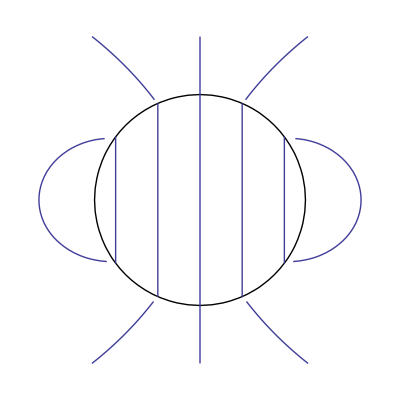

```mathematica
(*Export["~/Dokumentumok/Pk.png",*)Show[ContourPlot[x^2+y^2==1,{x,-1.55,1.55},{y,-1.55,1.55},ContourStyle->{Black,Thick}],StreamPlot[Emm[x,y,1,3],{x,-1.55,1.55},{y,-1.55,1.55},
StreamScale->Full,
StreamStyle->{"Line",Thick},
StreamPoints->{pointsb,Automatic}],Frame->None]
```

```mathematica
Export["~/Dokumentumok/Db.png",
Show[ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->{Black,Filling->Bottom,Thick}],StreamPlot[Evv[x,y,3,1],{x,-1.5,1.5},{y,-1.5,1.5},
StreamScale->Full,
StreamStyle->{"Line",Thick},
StreamPoints->{points2,Automatic,10}],Frame->None],ImageResolution->300]
Export["~/Dokumentumok/Eb.png",
Show[ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->{Black,Filling->Bottom,Thick},Background->None],Graphics[{White,Disk[{0,0},1]}],ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->{Black,Filling->Bottom,Thick},Background->None],StreamPlot[Evvb[x,y,3,1],{x,-1.5,1.5},{y,-1.5,1.5},StreamScale->Full,
StreamStyle->{"Line",Thick},
StreamPoints->{pointsE2,Automatic,10},PerformanceGoal->"Quality",Background->None],Frame->None,Background->None],Background->None,ImageResolution->300]
```

~/Dokumentumok/Db.png

~/Dokumentumok/Eb.png

Mágneses rész következik

```mathematica
Export["~/Dokumentumok/diaH.pdf",Show[ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->{Black}],StreamPlot[Evv[x,y,0,1],{x,-1.5,1.5},{y,-1.5,1.5},
StreamScale->Full,
StreamStyle->{"Arrow",Thick},
StreamPoints->{points2,Automatic}],Frame->None]]
Export["~/Dokumentumok/diaB.pdf",Show[ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->{Black}],StreamPlot[Evv[x,y,0,1]-3*M[x,y,0,1],{x,-1.5,1.5},{y,-1.5,1.5},
StreamScale->Full,
StreamStyle->{"Arrow",Thick},
StreamPoints->{points2,Automatic}],Frame->None]]
```

~/Dokumentumok/diaH.pdf

~/Dokumentumok/diaB.pdf

```mathematica
Export["~/Dokumentumok/ferroH.pdf",Show[ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->{Black}],StreamPlot[Evv[x,y,99999,1],{x,-1.5,1.5},{y,-1.5,1.5},
StreamScale->Full,
StreamStyle->{"Arrow",Thick},
StreamPoints->{points,Automatic}],Frame->None]]
Export["~/Dokumentumok/ferroB.pdf",Show[ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->{Black}],StreamPlot[Evv[x,y,99999,1]-3*M[x,y,99999,1],{x,-1.5,1.5},{y,-1.5,1.5},
StreamScale->Full,
StreamStyle->{"Arrow",Thick},
StreamPoints->{points,Automatic}],Frame->None]]
```

~/Dokumentumok/ferroH.pdf

~/Dokumentumok/ferroB.pdf

```mathematica
Export["~/Dokumentumok/diamomentum.pdf",Show[ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->{Black}],StreamPlot[Emm[x,y,0,1],{x,-1.5,1.5},{y,-1.5,1.5},
StreamScale->Full,
StreamStyle->{"Arrow",Thick},
StreamPoints->{points2,Automatic}],Frame->None]]
Export["~/Dokumentumok/ferromomentum.pdf",Show[ContourPlot[x^2+y^2==1,{x,-1.5,1.5},{y,-1.5,1.5},ContourStyle->{Black}],StreamPlot[Emm[x,y,99999,1],{x,-1.5,1.5},{y,-1.5,1.5},
StreamScale->Full,
StreamStyle->{"Arrow",Thick},
StreamPoints->{points2,Automatic}],Frame->None]]
```

~/Dokumentumok/diamomentum.pdf

~/Dokumentumok/ferromomentum.pdf